# NoteBook for Reissner - Nordstrom metric for the TT-modes.

This notebook will compute the QNMs, potential and absorption probabilities for the Reissner-Nordstrom metric in any number of dimensions for spin-3/2 fields for the TT related modes. This notebook is coded to allow for multi threaded processing of the QNMs, this speeds up the amount of time take to compute all the QNMS.

## Setup

First clear global variables, then set up the number of iterations performed by the AIM, and finally define the mass of the black hole. We have always used m = 1.

```mathematica
Remove["Global`*"];
nmax=200; (*Number of iterations*)
TotM = 1;(*Black hole mass*)
TotΛ = 0; (* Asymtoptic curvature of space time*)
Names["Global`*"]
(* metric function*)
```

{nmax,TotM,TotΛ}

## The Routines

### Seed table

First we setup the Seed table function which provides the seed values for the QNM calculations. It can also be used to determine the absorption probabilities. Inputs are, quantum numbers l and n, Charge and total number of dimensions of the metric. The format is the following
“WKBSeedTable[ElectricCharge, Number of Total Dimensions]”= {{l=0 and n=0},{l=1 and n=0, l=1 and n=1}, {l=2 and n=0,l=2 and n=1,l=2 and n=2},....}. The AIMSeed table follows the same format.

```mathematica
(*The procedure returns seeding values for the WKB method*)(*Requires the l is the angular mode, n is the mode and TotDim is the number of dimesnions you are looking at*)
WKBSeed[l_,n_,TotQ_,TotDim_] := Module[{WKBSeedTable},
(*Charge = 0*)
WKBSeedTable[0,4]={{0.3800-0.0963ⅈ},{0.5740-0.0963ⅈ,0.5570-0.2927ⅈ},{0.7673-0.0962ⅈ,0.7543-0.2909ⅈ,0.7297-0.4919ⅈ},{0.9602-0.0962ⅈ ,0.9497-0.2901ⅈ,0.9294-0.4881ⅈ,0.9010-0.6925ⅈ},{1.1530-0.0962ⅈ,1.1442-0.2897 ⅈ,1.1270-0.4860ⅈ,1.1024-0.6869ⅈ,1.0717-0.8938ⅈ},{1.3457-0.0962ⅈ,1.3381-0.2894ⅈ,1.3233-0.4847ⅈ,1.3017-0.6834ⅈ,1.2743-0.8867ⅈ,1.2421-1.0957ⅈ}};
WKBSeedTable[0,5]={{0.8665-0.2509ⅈ},{1.2247-0.2504ⅈ,1.1512-0.7681ⅈ},{1.5812-0.2501ⅈ,1.5232-0.7605ⅈ,1.4130-1.3016ⅈ},{1.9365-0.2500ⅈ,1.8888-0.7569ⅈ,1.7963-1.2841ⅈ,1.6657-1.8455ⅈ},{2.2913-0.2500ⅈ,2.2508-0.7549ⅈ,2.1715-1.2742ⅈ,2.0573-1.8181ⅈ,1.9142-2.3960ⅈ},{2.6457-0.2500ⅈ,2.6106-0.7536ⅈ,2.5413-1.2681ⅈ,2.4404-1.8009ⅈ,2.3117-2.3595ⅈ,2.1604-2.9506ⅈ}};       
WKBSeedTable[0,6]={{1.3244-0.3984ⅈ},{1.7864-0.3941ⅈ,1.6274-1.2177 ⅈ},{2.2453-0.3926ⅈ,2.1180-1.1984ⅈ,1.8660-2.0722ⅈ},{2.7016-0.3923ⅈ,2.5958-1.1905ⅈ,2.3844-2.0329ⅈ,2.0726-2.9588ⅈ},{3.1569-0.3923ⅈ,3.0662-1.1866ⅈ,2.8848-2.0120ⅈ,2.6145-2.8956ⅈ,2.2631-3.8696ⅈ},{3.6116-0.3923ⅈ,3.5323-1.1842ⅈ,3.3734-1.9994ⅈ,3.1358-2.8573 ⅈ,2.8235-3.7812ⅈ,2.4448-4.7973ⅈ}};
WKBSeedTable[0,7]={{1.7657-0.5430ⅈ},{2.3050-0.5280ⅈ,2.0338-1.6461ⅈ},{2.8382-0.5224ⅈ,2.6204-1.6001ⅈ,2.1674-2.7923ⅈ},{3.3652-0.5215ⅈ,3.1838-1.5841ⅈ,2.8061-2.7164ⅈ,2.2179-4.0012ⅈ},{3.8903-0.5215ⅈ,3.7340-1.5781ⅈ,3.4110-2.6817ⅈ,2.9073-3.8866ⅈ,2.2238-5.2718ⅈ},{4.4146-0.5215ⅈ,4.2770-1.5749ⅈ,3.9946-2.6628ⅈ,3.5560-3.8222ⅈ,2.9553-5.1089ⅈ,2.2048-6.5907ⅈ}};
WKBSeedTable[0,8]={{2.1898-0.6925ⅈ},{2.7967-0.6567ⅈ,2.3847-2.0788ⅈ},{3.3924-0.6419ⅈ,3.0616-1.9775ⅈ,2.3470-3.4828ⅈ},{3.9730-0.6395ⅈ,3.7005-1.9424ⅈ,3.1068-3.3392ⅈ,2.1355-4.9655ⅈ},{4.5500-0.6395ⅈ,4.3149-1.9331ⅈ,3.8106-3.2829ⅈ,2.9838-4.7786ⅈ,1.8201-6.5681ⅈ},{5.1260-0.6397ⅈ,4.9181-1.9298ⅈ,4.4788-3.2587ⅈ,3.7654-4.6844ⅈ,2.7466-6.3146ⅈ,1.4472-8.2785ⅈ}};
WKBSeedTable[0,9] ={{2.5919-0.8545ⅈ},{3.2660-0.7850ⅈ,2.6821-2.5471ⅈ},{3.9226-0.7534ⅈ,3.4510-2.3491ⅈ,2.4234-4.1760ⅈ},{4.5473-0.7480ⅈ,4.1687-2.2720ⅈ,3.3075-3.9155ⅈ,1.8499-5.8379ⅈ},{5.1646-0.7480ⅈ,4.8397-2.2551ⅈ,4.1142-3.8159ⅈ,2.8660-5.5549 ⅈ,1.0532-7.6865 ⅈ},{5.7807-0.7487ⅈ,5.4923-2.2524ⅈ,4.8636-3.7856ⅈ,3.7927-5.4233ⅈ,2.1983-7.3427ⅈ,0.1316-9.7374ⅈ}};
(*Charge = 0.1*)
WKBSeedTable[0.1,4]={{0.3742-0.0958ⅈ},{0.5686-0.0960ⅈ,0.5513-0.2918ⅈ},{0.7622-0.0960ⅈ,0.7490-0.2903ⅈ,0.7243-0.4909ⅈ},{0.9554-0.0960ⅈ,0.9448-0.2896ⅈ,0.9244-0.4873ⅈ,0.8959-0.6915ⅈ},{1.1485-0.0961ⅈ,1.1397-0.2893ⅈ,1.1224-0.4854ⅈ,1.0977-0.6861ⅈ,1.0669-0.8928ⅈ},{1.3415-0.0961ⅈ,1.3339-0.2891ⅈ,1.3190-0.4842ⅈ,1.2974-0.6828 ⅈ,1.2699-0.8860ⅈ,1.2376-1.0948ⅈ}};
WKBSeedTable[0.1,5]={{0.8537-0.2492ⅈ},{1.2123-0.2490ⅈ,1.1384-0.7640ⅈ},{1.5690-0.2490ⅈ,1.5108-0.7572ⅈ,1.4002-1.2962ⅈ},{1.9245-0.2492ⅈ,1.8767-0.7541ⅈ,1.7840-1.2795ⅈ,1.6530-1.8392ⅈ},{2.2795-0.2493ⅈ,2.2390-0.7525ⅈ,2.1596-1.2703ⅈ,2.0451-1.8126ⅈ,1.9017-2.3890ⅈ},{2.6342-0.2493ⅈ,2.5990-0.7516ⅈ,2.5297-1.2647ⅈ,2.4286-1.7961ⅈ,2.2998-2.3533ⅈ,2.1482-2.9430ⅈ}};
WKBSeedTable[0.1,6]={{1.3063-0.3961ⅈ},{1.7692-0.3917ⅈ,1.6097-1.2106ⅈ},{2.2281-0.3906ⅈ,2.1008-1.1922 ⅈ,1.8483-2.0618ⅈ},{2.6846-0.3906ⅈ,2.5787-1.1853ⅈ,2.3672-2.0240ⅈ,2.0549-2.9462ⅈ},{3.1400-0.3908 ⅈ,3.0493-1.1821ⅈ,2.8678-2.0044ⅈ,2.5975-2.8847ⅈ,2.2457-3.8554ⅈ},{3.5948-0.3910ⅈ,3.5156-1.1802 ⅈ,3.3567-1.9926 ⅈ,3.1191-2.8476ⅈ,2.8067-3.7686ⅈ,2.4278-4.7818ⅈ}};WKBSeedTable[0.1,7]={{1.7430-0.5408 ⅈ},{2.2844-0.5247ⅈ,2.0126-1.6368ⅈ},{2.8176-0.5196ⅈ, 2.6000-1.5911ⅈ,2.1468-2.7766ⅈ},{3.3445-0.5191ⅈ,3.1633-1.5766ⅈ,2.7858-2.7031ⅈ,2.1975-3.9815ⅈ},{3.8696-0.5194ⅈ,3.7135-1.5716ⅈ,3.3908-2.6705ⅈ,2.8874-3.8700ⅈ,2.2039-5.2494ⅈ},{4.3940-0.5197ⅈ,4.2566-1.5691ⅈ,3.9746-2.6529ⅈ,3.5363-3.8079ⅈ,2.9360-5.0898ⅈ,2.1857-6.5663 ⅈ}};
WKBSeedTable[0.1,8]={{2.1629-0.6911ⅈ},{2.7739-0.6523ⅈ,2.3607-2.0685ⅈ},{3.3693-0.6382ⅈ,3.0396-1.9651ⅈ,2.3253-3.4612ⅈ},{3.9496-0.6365ⅈ,3.6779-1.9325ⅈ,3.0851-3.3204ⅈ,2.1144-4.9367ⅈ},{4.5265-0.6369ⅈ,4.2919-1.9247ⅈ,3.7886-3.2678ⅈ,2.9627-4.7553ⅈ,1.7996-6.5355ⅈ},{5.1025-0.6374ⅈ,4.8950-1.9225ⅈ,4.4565-3.2459ⅈ,3.7441-4.6651ⅈ,2.7263-6.2878ⅈ ,1.4279-8.2431ⅈ}};
WKBSeedTable[0.1,9] ={{2.5610-0.8542ⅈ},{3.2421-0.7794ⅈ,2.6560-2.5372 ⅈ},{3.8980-0.7488ⅈ, 3.4291-2.3324ⅈ,2.4026-4.1484 ⅈ},{4.5219-0.7443ⅈ,4.1453-2.2591ⅈ,3.2863-3.8889ⅈ,1.8298-5.7974ⅈ},{5.1390-0.7449ⅈ,4.8151-2.2449ⅈ,4.0916-3.7959ⅈ,2.8450-5.5217ⅈ,1.0327-7.6402ⅈ},{5.7549-0.7459ⅈ,5.4672-2.2437ⅈ,4.8401-3.7696ⅈ,3.7711-5.3977ⅈ,2.1779-7.3055ⅈ,0.1122-9.6880ⅈ}};
(*Charge = 0.5 *)
WKBSeedTable[0.5,4]={{0.3625-0.0947ⅈ},{0.5653-0.0956ⅈ,0.5480-0.2907ⅈ},{0.7673-0.0960ⅈ,0.7543-0.2903ⅈ,0.7299-0.4908ⅈ},{0.9690-0.0963ⅈ,0.9587-0.2903ⅈ,0.93880-0.4884ⅈ,0.9108-0.6927ⅈ},{1.1706-0.0965ⅈ,1.1620-0.2905ⅈ,1.1452-0.4872ⅈ,1.1212-0.6885ⅈ,1.0912-0.8956ⅈ},{1.3721-0.0966ⅈ,1.3648-0.2906ⅈ,1.3504-0.4867ⅈ,1.3294-0.6860ⅈ,1.3028-0.8898ⅈ,1.2715-1.0990ⅈ}};WKBSeedTable[0.5,5]={{0.8130-0.2411ⅈ},{1.1768-0.2418ⅈ,1.1045-0.7419ⅈ},{1.5387-0.2428ⅈ,1.4825-0.7381ⅈ,1.3754-1.2628ⅈ},{1.8996-0.2436ⅈ,1.8537-0.7372ⅈ,1.7647-1.2502ⅈ,1.6389-1.7957ⅈ},{2.2601-0.2442ⅈ,2.2213-0.7370ⅈ,2.1454-1.2437ⅈ,2.0361-1.7736ⅈ,1.8992-2.3356ⅈ},{2.6203-0.2446ⅈ,2.5867-0.7372ⅈ,2.5207-1.2400ⅈ,2.4245-1.7603ⅈ,2.3020-2.3048ⅈ,2.1580-2.8799ⅈ}};
WKBSeedTable[0.5,6]={{1.2484-0.3816ⅈ},{1.7124-0.3790ⅈ,1.5568-1.1692ⅈ},{2.1739-0.3794ⅈ,2.0504-1.1572ⅈ, 1.8052-1.9976ⅈ},{2.6335-0.3804ⅈ,2.5313-1.1538ⅈ,2.3273-1.9684ⅈ,2.0259-2.8605ⅈ},{3.0923-0.3813ⅈ,3.0051-1.1529ⅈ,2.8307-1.9537ⅈ,2.5712-2.8088ⅈ,2.2336-3.7479ⅈ},{3.5506-0.3819 ⅈ,3.4746-1.1527ⅈ,3.3224-1.9454ⅈ,3.0951-2.7781ⅈ,2.7965-3.6724ⅈ,2.4344-4.6523 ⅈ}};WKBSeedTable[0.5,7]={{1.6769-0.5175ⅈ},{2.2147-0.5067ⅈ,1.9497-1.5713ⅈ},{2.7474-0.5046ⅈ,2.5363-1.5413ⅈ,2.0923-2.6761ⅈ},{3.2757-0.5056ⅈ,3.1001-1.5339ⅈ,2.7337-2.6236ⅈ,2.1600-3.8499ⅈ},{3.8028-0.5067ⅈ,3.6518-1.5324ⅈ,3.3398-2.6008ⅈ,2.8530-3.7610ⅈ,2.1898-5.0856ⅈ},{4.3294-0.5076ⅈ,4.1967-1.5323ⅈ,3.9248-2.5888ⅈ,3.5026-3.7110ⅈ,2.9241-4.9499ⅈ,2.1989-6.3684ⅈ}};        WKBSeedTable[0.5,8]={{2.0917-0.6572ⅈ},{2.6975-0.6278ⅈ,2.2926-1.9698ⅈ},{3.2886-0.6197ⅈ,2.9691-1.8968ⅈ,2.2619-3.3068ⅈ},{3.8684-0.6204ⅈ,3.6043-1.8792ⅈ,3.0258-3.2118ⅈ,2.0667-4.7396ⅈ},{4.4462-0.6220ⅈ,4.2182-1.8777ⅈ,3.7290-3.1800ⅈ,2.9239-4.6074ⅈ,1.7796-6.2975ⅈ},{5.0236-0.6232ⅈ,4.8220-1.8787ⅈ,4.3969-3.1679ⅈ,3.7064-4.5418ⅈ,2.7163-6.0985ⅈ,1.4440-7.9607ⅈ}};
WKBSeedTable[0.5,9] ={{2.4845-0.8095ⅈ},{3.1639-0.7465ⅈ,2.5829-2.3982ⅈ},{3.8107-0.7263ⅈ,3.3582-2.2375ⅈ,2.3289-3.9152ⅈ},{4.4317-0.7261ⅈ,4.0659-2.1930ⅈ,3.2238-3.7363ⅈ,1.7612-5.4995ⅈ},{5.0486-0.7284ⅈ,4.7329-2.1905ⅈ,4.0274-3.6856ⅈ,2.8012-5.3165ⅈ,0.9867-7.2938ⅈ},{5.6653-0.7302ⅈ,5.3848-2.1944ⅈ,4.7743-3.6779ⅈ,3.7322-5.2418ⅈ,2.1651-7.0476ⅈ,0.1075-9.2911ⅈ}};
       (*Charge = 1*)
WKBSeedTable[1,4]={{0.3777-0.0893ⅈ},{0.6265-0.0887ⅈ,0.6081-0.2691ⅈ},{0.8761-0.0885ⅈ,0.8628-0.2671ⅈ,0.8367-0.4501ⅈ},{1.1258-0.0885ⅈ,1.1155-0.2663ⅈ,1.0950-0.4468ⅈ,1.0648-0.6318ⅈ},{1.3757-0.0884ⅈ,1.3672-0.2659ⅈ,1.3503-0.4452ⅈ,1.3253-0.6275ⅈ,1.2926-0.8140ⅈ},{1.6256-0.0884ⅈ,1.6184-0.2657ⅈ,1.6041-0.4443ⅈ,1.5828-0.6250ⅈ,1.5547-0.8087ⅈ,1.5203-0.9962ⅈ}};WKBSeedTable[1,5]={{0.7748-0.2266ⅈ},{1.1578-0.2242ⅈ,1.0827-0.6866ⅈ},{1.5420-0.2233ⅈ,1.4853-0.6776ⅈ,1.3734-1.1563ⅈ},{1.9264-0.2229ⅈ,1.8809-0.6735ⅈ,1.7906-1.1393ⅈ,1.6574-1.6323ⅈ},{2.3110-0.2227ⅈ,2.2731-0.6714ⅈ,2.1975-1.1304ⅈ,2.0852-1.6076ⅈ,1.9383-2.1120ⅈ},{2.6957-0.2226ⅈ,2.6631-0.6701ⅈ,2.5982-1.1252ⅈ,2.5014-1.5932ⅈ,2.3738-2.0806ⅈ,2.2176-2.5942ⅈ}};
WKBSeedTable[1,6]={{1.1816-0.3674ⅈ},{1.6557-0.3593ⅈ,1.4941-1.1081ⅈ},{2.1282-0.3568ⅈ,2.0037-1.0867ⅈ,1.7499-1.8733ⅈ},{2.6003-0.3559ⅈ,2.4990-1.0780ⅈ,2.2927-1.8346ⅈ,1.9791-2.6610ⅈ},{3.0725-0.3555ⅈ,2.9869-1.0736ⅈ,2.8134-1.8150ⅈ,2.5492-2.6021ⅈ,2.1950-3.4647ⅈ},{3.5448-0.3552ⅈ,3.4707-1.0709ⅈ,3.3209-1.8036ⅈ,3.0932-2.5684ⅈ,2.7864-3.3853ⅈ,2.4036-4.2794ⅈ}};
WKBSeedTable[1,7]={{1.5886-0.5104ⅈ},{2.1369-0.4882ⅈ,1.8602-1.5197ⅈ},{2.6752-0.4824ⅈ,2.4613-1.4728ⅈ,2.0051-2.5593ⅈ},{3.2103-0.4809ⅈ,3.0353-1.4574ⅈ,2.6659-2.4884ⅈ,2.0774-3.6483ⅈ},{3.7452-0.4803ⅈ,3.5963-1.4508ⅈ,3.2860-2.4568ⅈ,2.7943-3.5431ⅈ,2.1118-4.7819ⅈ},{4.2801-0.4799ⅈ,4.1502-1.4471ⅈ,3.8824-2.4397ⅈ,3.4614-3.4866ⅈ,2.8744-4.6353ⅈ,2.1250-5.9489ⅈ}};        WKBSeedTable[1,8]={{1.9870-0.6602ⅈ},{2.6068-0.6121ⅈ,2.1835-1.9362ⅈ},{3.2001-0.5995ⅈ,2.8756-1.8360ⅈ,2.1526-3.2127ⅈ},{3.7835-0.5971ⅈ,3.5194-1.8075ⅈ,2.9366-3.0873ⅈ,1.9630-4.5594ⅈ},{4.3658-0.5965ⅈ,4.1401-1.7991ⅈ,3.6535-3.0412ⅈ,2.8447-4.3961ⅈ,1.6830-5.9997ⅈ},{4.9481-0.5961ⅈ,4.7502-1.7953ⅈ,4.3310-3.0211ⅈ,3.6448-4.3174ⅈ,2.6490-5.7760ⅈ,1.3532-7.5184ⅈ}};
WKBSeedTable[1,9] ={{2.3683-0.8228ⅈ},{3.0664-0.7333ⅈ,2.4603-2.3848ⅈ},{3.7120-0.7085ⅈ,3.2525-2.1853 ⅈ,2.2046-3.8491ⅈ},{4.3342-0.7048ⅈ,3.9670-2.1288 ⅈ,3.1191-3.6290ⅈ,1.6452-5.3558ⅈ},{4.9535-0.7045ⅈ,4.6398-2.1175ⅈ,3.9371-3.5585ⅈ,2.7096-5.1251ⅈ,0.8842-7.0235ⅈ},{5.5730-0.7044ⅈ,5.2965-2.1153ⅈ,4.6936-3.5390ⅈ,3.6600-5.0277ⅈ,2.0919-6.7328ⅈ,0.0139-8.8472ⅈ}};
Return[WKBSeedTable[TotQ,TotDim][[l+1,n+1]]]];
```

### The beta function.

This is the β function used by the AIM to stop the results from blowing up to infinity.These functions need to be calculated by hand, but are then just plugged into the method. These need to be calculated separately for each new value of M, Q and Λ, when we introduce the asymptotic curvature. Input is the charge and number of dimensions, the output is a function dependent on ξ, which is related to r, and ω, the QNM.

```mathematica
(* Returns the Beta function used by the AIM*) (*Returns the function in the form of β[ξ,ω], requires the number of dimensions of the current spacetime*)(*These have to be recalculated for diffirent values of M, Q and Λ *)
BetaFunction[TotDim_,TotQ_,ξ_,ω_] := Module[{β},
(*Q=0*)
β[0,4]=(1-ξ^(2))^(-2×ⅈ×ω)*(ξ^(2))^(-ⅈ×2*ω)×ⅇ^(ⅈ×ω×2×(1-ξ^(2))^-1);
β[0,5]=  ⅇ^((Sqrt[2]*ⅈ*ω)/(1 - ξ^2))(ξ^(2))^(-((ⅈ*ω)/Sqrt[2]));
β[0,6] =ⅇ^((ⅈ*ω*2^(1/3))/(1-ξ^(2)))(1-ξ^(2))^(-((ⅈ*ω*2^(1/3))/(3)))(ξ^(2))^(-((ⅈ*ω*2^(1/3))/(3)))((1-ξ^(2))^(2))^(-ⅈ*ω*(1/(3*2^(2/3)))) ;
β[0,7]= ⅇ^((ⅈ*ω*2^(1/4))/(1-ξ^(2)))(1-ξ^(2))^(-((ⅈ*ω)/(2*2^(3/4))))(ξ^(2))^(-((ⅈ*ω)/(2*2^(3/4))));
β[0,8] = ⅇ^((ⅈ*ω*2^(1/5))/(1-ξ^(2)))(ξ^(2))^(-ⅈ*ω*((4)/(10*2^(4/5))))(1-ξ^(2))^(-ⅈ*ω*(4/(10*2^(4/5))))((1-ξ^(2))^(2))^(((-1+Sqrt[5])/(10*2^(4/5)))(-ⅈ*ω));
β[0,9]=ⅇ^((ⅈ*ω*2^(1/6))/(1-ξ^(2)))(1-ξ^(2))^(-((ⅈ*ω)*(((2)^(1/6))/(6))))(ξ^(2))^(-((ⅈ*ω)*(((2)^(1/6))/(6))));
(*Q=0.1*)
β[0.1,4] =ⅇ^((ⅈ*ω(1.99498))/(1-ξ^(2)))(1-ξ^(2))^(-(ⅈ*ω)(316804/158401))(ξ^(2))^(-(ⅈ*ω)(316804/158401))(1-ξ^(2))^(-ⅈ*ω*(0.0000126261));
β[0.1,5] =ⅇ^((1.41244)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-(0.0000891686)(ⅈ*ω))(ξ^(2))^(-(0.707999)(ⅈ*ω))(1-ξ^(2))^(-(0.707999)(ⅈ*ω));
β[0.1,6] =ⅇ^((1.25886)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-0.000143695*ⅈ*ω)((1-ξ^(2))^(2))^(-ⅈ*ω*0.0000718479)(ξ^(2))^(-0.42067*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*(0.42067))((1-ξ^(2))^(2))^(-ⅈ*ω*(0.21033));
β[0.1,7]=  ⅇ^((1.18846)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-0.000167558*ⅈ*ω)(ξ^(2))^(-0.297863*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*(0.297863));
β[0.1,8]= ⅇ^((1.14812)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-(0.000174684)*ⅈ*ω)((1-ξ^(2))^(2))^(-ⅈ*ω*0.0000539804)((1-ξ^(2))^(2))^(-ⅈ*ω*0.000141322)(ξ^(2))^(-(0.230202)*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*((0.230202)))((1-ξ^(2))^(2))^(-ⅈ*ω*(0.0711365))((1-ξ^(2))^(2))^(-ⅈ*ω*(0.186237));
β[0.1,9]=ⅇ^((1.12199)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-0.000173675*ⅈ*ω)((1-ξ^(2))^(2))^(-ⅈ*ω*0.0000868375)((1-ξ^(2))^(2))^(-ⅈ*ω*0.0937349)(1-ξ^(2))^(-ⅈ*ω*0.18746)(ξ^(2))^(-ⅈ*ω*0.18746);
(*Q=0.5*)
β[0.5,4] =ⅇ^((ⅈ*ω(1.86603))/(1-ξ^(2)))(1-ξ^(2))^(-(ⅈ*ω)(2.01036))(ξ^(2))^(-(ⅈ*ω)(2.01036));
β[0.5,5] =ⅇ^((1.36602)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-(0.0141560)(ⅈ*ω))(ξ^(2))^(-(0.0141560)(ⅈ*ω))(1-ξ^(2))^(-ⅈ*ω*0.735843);
β[0.5,6] =ⅇ^((1.23113)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-ⅈ*ω*(0.013191))((1-ξ^(2))^(2))^(-ⅈ*ω*(0.006596))((1-ξ^(2))^(2))^(-ⅈ*ω*(0.221061))(1-ξ^(2))^(-0.442121*ⅈ*ω)(ξ^(2))^(-0.442121*ⅈ*ω);
β[0.5,7]= ⅇ^((1.168770)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-0.011699*ⅈ*ω)(ξ^(2))^(-0.314793*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*(0.314793));
β[0.5,8]=ⅇ^((1.132878)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-0.010349*ⅈ*ω)((1-ξ^(2))^(2))^(-ⅈ*ω*(0.003198))((1-ξ^(2))^(2))^(-ⅈ*ω*(0.00837247))(ξ^(2))^(-0.244101*ⅈ*ω)(1-ξ^(2))^(-ⅈ*ω*0.244101)((1-ξ^(2))^(2))^(-ⅈ*ω*0.0754315)((1-ξ^(2))^(2))^(-ⅈ*ω*0.197482);
β[0.5,9]=ⅇ^((1.10956)((ⅈ*ω)/(1-ξ^(2))))(1-ξ^(2))^(-ⅈ*ω*(0.009221))((1-ξ^(2))^(2))^(-ⅈ*ω*(0.004610))((1-ξ^(2))^(2))^(-ⅈ*ω*(0.099615))(ξ^(2))^(-ⅈ*ω*(0.19923))((1-ξ^(2)))^(-ⅈ*ω*(0.19923));
(*Q=1*)
β[1,4] =ⅇ^((ⅈ*ω)/(1-ξ^(2)))ⅇ^(ⅈ*ω*(1-ξ^(2))/(ξ^(2)))(ξ^(2))^(-(2*ⅈ*ω))(1-ξ^(2))^(-(2*ⅈ*ω));
β[1,5] =ⅇ^(((ⅈ*ω)/(1-ξ^(2))))ⅇ^((ⅈ*ω*(1-ξ^(2)))/(ξ(2-ξ)))(ξ^(2))^(-((3*ⅈ*ω)/4));
β[1,6] =ⅇ^((ⅈ*ω)/(1-ξ^(2)))ⅇ^((ⅈ*ω*(1-ξ^(2))^(2))/(3(1-(1-ξ^(2))^(3))))(ξ^(2))^(-(4*ⅈ*ω)/(9))(1-ξ^(2))^(-(4*ⅈ*ω)/(9));
β[1,7]= ⅇ^((ⅈ*ω)/(1-ξ^(2)))ⅇ^((ⅈ*ω*(1-ξ^(2))^(3))/(4(1-(1-ξ^(2))^(4))))(ξ^(2))^((-5*ⅈ*ω)/(16))(1-ξ^(2))^((-5*ⅈ*ω)/(16));
β[1,8]=ⅇ^((ⅈ*ω)/(1-ξ^(2)))ⅇ^((ⅈ*ω*(1-ξ^(2))^(4))/(5(1-(1-ξ^(2))^(5))))(ξ^(2))^(-(12*ⅈ*ω)/(50))(1-ξ^(2))^(-(12*ⅈ*ω)/(50))((1-ξ^(2))^(2))^(-((3(-1+Sqrt[5])*ⅈ*ω))/(50))((1-ξ^(2))^(2))^(-((3(1+Sqrt[5])ⅈ*ω)/(50))) ;
β[1,9]=ⅇ^((ⅈ*ω)/(1-ξ^(2)))ⅇ^((12*ⅈ*ω*(1-ξ^(2))^(5))/(72(1-(1-ξ^(2))^(6))))(ξ^(2))^(-(14*ⅈ*ω)/(72))(1-ξ^(2))^(-(14*ⅈ*ω)/(72));
Return[β[TotQ,TotDim]]];
```

#### The WKB method to 3 rd order

This routine for calculating the QNM using WKB to 3 rd order. The inputs are l, n, the electric charge and the number of Dimensions. The output is simply the complex QNM. This has been written to allow for multi threading, it must be left in the Module[] command otherwise it will not work. The variables are all cleared at the end of the routine to prevent memory access problems.

```mathematica
(*This is the actaul method for calculating the WKB results, it returns only a number*)(*The input required is the angular mode and the n mode aswell as the current number of dimensions*)
WKBMethod3rd[l_,n_,TotQ_,TotDim_] :=Module[ {r,f,ω,j,DiffV,barζ,CC,AA,BB,W,V,r0,ω0=WKBSeed[l,n,TotQ,TotDim],Q,α,p,Λ,Ω,R,W1,W2,W3,RootSeed},
barζ= (l+3/2)+(TotDim-3)/(2); (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))-((2*TotΛ*r^(2))/((TotDim-2)(TotDim-1)))+((TotQ^(2))/r^(2*TotDim -6));(*Metric function*)
 (* This begins the WKB approximation, none of this should ever need to be changed*)
α[p_]:=p+1/2;
Λ[2][ω_,p_]:=Simplify[(ⅈ/(2×Q[2][r,ω])^(1/2)×(1/8×((Q[4][r,ω])/(Q[2][r,ω]))×(α[p]^2+1/4)- 1/288×(7 +60×α[p]^2)×((Q[3][r,ω])/(Q[2][r,ω]))^2))/.{r->r0}];
Λ[3][ω_,p_]:=Simplify[ (α[p] +α[p]/(2×(Q[2][r,ω]))(5/6912×(((Q[3][r,ω])/(Q[2][r,ω]))^4)×(77 +188×α[p]^2)-1/384×(((Q[4][r,ω])×((Q[3][r,ω]))^2)/((Q[2][r,ω]))^3)×(51 +100×α[p]^2) + 1/2304×(((Q[4][r,ω])/(Q[2][r,ω]))^2)×(67 + 68×α[p]^2) +1/288×(((Q[5][r,ω])×((Q[3][r,ω])))/((Q[2][r,ω]))^2)×(19 +28×α[p]^2) -  1/288×((Q[6][r,ω])/(Q[2][r,ω]))×(5 + 4×α[p]^2)))/.{r->r0}];
Ω[3][ω_,p_]:=Simplify[ⅈ×(Q[0][r0,ω])/(2×Q[2][r0,ω])^(1/2)-Λ[2][ω,p]-Λ[3][ω,p]];
(*End of approximation*)
(*Paste potential between these two comments*)
        W[r_] =(barζ*Sqrt[f[r]])/(r)-((TotQ*Sqrt[f[r]])/(2*r^(TotDim-2)))(TotDim-2); (*I have split up this part to reduce the computatuion time*)
V[r_] =f[r]*D[W[r],r]+(W[r])^(2);(* non-TT potential*)
(*Paste potential here *)
DiffV[r_] = Rationalize[D[V[r],r]];
r0=First[Sort[r/.NSolve[DiffV[r]==0,r,Reals],Greater]];(*Our r0 values seem to have a maximum of 2.5. r0 going from zero to four here is to reduce computation time*)(*This may have to change for diffirent values of M*)
Q[0][r_,ω_]=ω^2-V[r];
Q[1][r_,ω_]=Simplify[ f[r]×D[Q[0][r,ω],r]];
Do[Q[q+1][r_,ω_]=Simplify[ f[r]×D[Q[q][r,ω],r]],{q,11}];
Λ[2][ω,n];
Λ[3][ω,n];
Ω[3][ω,n];
Return[ω/. FindRoot[Ω[3][ω,n],{ω,ω0},AccuracyGoal->5,PrecisionGoal->5]];
Clear[r,f,ω,j,DiffV,barζ,CC,AA,BB,W,V,r0,ω0,Q,α,p,Λ,Ω,R,W1,W2,W3,RootSeed];];

(* Works in the same way as the WKB3rd method*)
WKBMethod6th[l_,n_,TotQ_,TotDim_] :=Module[ {r,ω,f,j,barζ,CC,AA,BB,W,V,r0,ω0=WKBSeed[l,n,TotQ,TotDim],DiffV,Q,α,p,Λ,Ω,R,W1,W2,W3,RootSeed},
barζ= (l+3/2)+(TotDim-3)/(2); (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))-((2*TotΛ*r^(2))/((TotDim-2)(TotDim-1)))+((TotQ^(2))/r^(2*TotDim -6)); (*Metric function*)
(* This begins the WKB approximation, none of this should ever need to be changed*)
α[p_]:=p+1/2;
Λ[2][ω_,p_]:=Simplify[(ⅈ/(2×Q[2][r,ω])^(1/2)×(1/8×((Q[4][r,ω])/(Q[2][r,ω]))×(α[p]^2+1/4)- 1/288×(7 +60×α[p]^2)×((Q[3][r,ω])/(Q[2][r,ω]))^2))/.{r->r0}];
Λ[3][ω_,p_]:=Simplify[ (α[p] +α[p]/(2×(Q[2][r,ω]))(5/6912×(((Q[3][r,ω])/(Q[2][r,ω]))^4)×(77 +188×α[p]^2)-1/384×(((Q[4][r,ω])×((Q[3][r,ω]))^2)/((Q[2][r,ω]))^3)×(51 +100×α[p]^2) + 1/2304×(((Q[4][r,ω])/(Q[2][r,ω]))^2)×(67 + 68×α[p]^2) +1/288×(((Q[5][r,ω])×((Q[3][r,ω])))/((Q[2][r,ω]))^2)×(19 +28×α[p]^2) -  1/288×((Q[6][r,ω])/(Q[2][r,ω]))×(5 + 4×α[p]^2)))/.{r->r0}];
Ω[3][ω_,p_]:=Simplify[ⅈ×(Q[0][r0,ω])/(2×Q[2][r0,ω])^(1/2)-Λ[2][ω,p]-Λ[3][ω,p]];
Λ[4][ω_,p_]:=Simplify[(1/(597196800 √2 ((Q[2][r,ω]))^7 √(Q[2][r,ω]))(ⅈ (2536975 ((Q[3][r,ω]))^6-9886275 ((Q[2][r,ω])) ((Q[3][r,ω]))^4 ((Q[4][r,ω]))+5319720 ((Q[2][r,ω]))^2 ((Q[3][r,ω]))^3 ((Q[5][r,ω]))-225 (Q[2][r,ω])^2 (Q[3][r,ω])^2 (-40261 (Q[4][r,ω])^2+9688 (Q[2][r,ω]) (Q[6][r,ω]))+3240 (Q[2][r,ω])^3 (Q[3][r,ω]) (-1889 (Q[4][r,ω]) (Q[5][r,ω])+220 (Q[2][r,ω]) (Q[7][r,ω]))-729 (Q[2][r,ω])^3 (1425 (Q[4][r,ω])^3-1400 (Q[2][r,ω]) (Q[4][r,ω]) (Q[6][r,ω])+8 (Q[2][r,ω]) (-123 (Q[5][r,ω])^2+25 (Q[2][r,ω]) (Q[8][r,ω])))))+1/(4976640 √2 ((Q[2][r,ω]))^7 √(Q[2][r,ω]))(ⅈ (348425 (Q[3][r,ω])^6-1199925 (Q[2][r,ω]) (Q[3][r,ω])^4 (Q[4][r,ω])+572760 (Q[2][r,ω])^2 (Q[3][r,ω])^3 (Q[5][r,ω])-45 (Q[2][r,ω])^2 (Q[3][r,ω])^2 (-20671 (Q[4][r,ω])^2+4552 (Q[2][r,ω]) (Q[6][r,ω]))+1080 (Q[2][r,ω])^3 (Q[3][r,ω]) (-489 (Q[4][r,ω]) (Q[5][r,ω])+52 (Q[2][r,ω]) (Q[7][r,ω]))-27 (Q[2][r,ω])^3 (2845 (Q[4][r,ω])^3-2360 (Q[2][r,ω]) (Q[4][r,ω]) (Q[6][r,ω])+56 (Q[2][r,ω]) (-31 (Q[5][r,ω])^2+5 (Q[2][r,ω]) (Q[8][r,ω])))) α[p]^2)+1/(2488320 √2 ((Q[2][r,ω]))^7 √(Q[2][r,ω]))  (ⅈ (192925 (Q[3][r,ω])^6-581625 (Q[2][r,ω]) (Q[3][r,ω])^4 (Q[4][r,ω])+234360 (Q[2][r,ω])^2 (Q[3][r,ω])^3 (Q[5][r,ω])-45 (Q[2][r,ω])^2 (Q[3][r,ω])^2 (-8315 (Q[4][r,ω])^2+1448 (Q[2][r,ω]) (Q[6][r,ω]))+1080 (Q[2][r,ω])^3 (Q[3][r,ω]) (-161 (Q[4][r,ω]) (Q[5][r,ω])+12 (Q[2][r,ω]) (Q[7][r,ω]))-27 (Q[2][r,ω])^3 (625 (Q[4][r,ω])^3-440 (Q[2][r,ω]) (Q[4][r,ω]) (Q[6][r,ω])+8 (Q[2][r,ω]) (-63 (Q[5][r,ω])^2+5 (Q[2][r,ω]) (Q[8][r,ω])))) α[p]^4))/.{r->r0}];
Λ[5][ω_,p_]:=Simplify[ (1/(7166361600 (Q[2][r,ω])^10)((1+2 n) (15552 (Q[10][r,ω]) (Q[2][r,ω])^7 (15+16 n+18 n^2+4 n^3+2 n^4)-720 (Q[2][r,ω])^2 (Q[3][r,ω])^5 (Q[5][r,ω]) (504060+1171942 n+1640011 n^2+936138 n^3+468069 n^4)-175 (Q[3][r,ω])^8 (916705+2411163 n+3552504 n^2+2282682 n^3+1141341 n^4)+300 (Q[2][r,ω]) (Q[3][r,ω])^6 (Q[4][r,ω]) (2493131+6188289 n+8909532 n^2+5442486 n^3+2721243 n^4)-4320 (Q[2][r,ω])^3 (Q[3][r,ω])^3 (8 (Q[2][r,ω]) (Q[7][r,ω]) (1306+2535 n+3270 n^2+1470 n^3+735 n^4)-5 (Q[4][r,ω]) (Q[5][r,ω]) (35282+75366 n+102603 n^2+54474 n^3+27237 n^4))+90 (Q[2][r,ω])^2 (Q[3][r,ω])^4 (8 (Q[2][r,ω]) (Q[6][r,ω]) (194828+416530 n+560485 n^2+287910 n^3+143955 n^4)-25 (Q[4][r,ω])^2 (459337+1060403 n+1485968 n^2+851130 n^3+425565 n^4))-27 (Q[2][r,ω])^4 (-80 (Q[2][r,ω]) (Q[4][r,ω])^2 (Q[6][r,ω]) (11220+16342 n+19471 n^2+6258 n^3+3129 n^4)+25 (Q[4][r,ω])^4 (30885+49927 n+60616 n^2+21378 n^3+10689 n^4)+32 (Q[2][r,ω])^2 (36 (Q[5][r,ω]) (Q[7][r,ω]) (199+288 n+354 n^2+132 n^3+66 n^4)+(Q[6][r,ω])^2 (3495+4538 n+5324 n^2+1572 n^3+786 n^4))+576 (Q[2][r,ω]) (Q[4][r,ω]) (15 (Q[2][r,ω]) (Q[8][r,ω]) (15+19 n+22 n^2+6 n^3+3 n^4)-(Q[5][r,ω])^2 (2196+3647 n+4676 n^2+2058 n^3+1029 n^4)))-432 (Q[2][r,ω])^4 (Q[3][r,ω]) (-240 (Q[2][r,ω]) (Q[4][r,ω]) (Q[7][r,ω]) (366+611 n+758 n^2+294 n^3+147 n^4)+25 (Q[4][r,ω])^2 (Q[5][r,ω]) (24692+46362 n+60621 n^2+28518 n^3+14259 n^4)+4 (Q[2][r,ω]) (5 (Q[2][r,ω]) (Q[9][r,ω]) (255+368 n+434 n^2+132 n^3+66 n^4)-(Q[5][r,ω]) (Q[6][r,ω]) (30107+51174 n+64992 n^2+27636 n^3+13818 n^4)))+540 (Q[2][r,ω])^3 (Q[3][r,ω])^2 (-24 (Q[2][r,ω]) (Q[4][r,ω]) (Q[6][r,ω]) (15498+29590 n+38515 n^2+17850 n^3+8925 n^4)+25 (Q[4][r,ω])^3 (31015+64549 n+87124 n^2+45150 n^3+22575 n^4)+8 (Q[2][r,ω]) (2 (Q[2][r,ω]) (Q[8][r,ω]) (1325+2263 n+2794 n^2+1062 n^3+531 n^4)-(Q[5][r,ω])^2 (28643+55916 n+74228 n^2+36624 n^3+18312 n^4))))))/.{r->r0}];
Λ[6][ω_,p_]:=Simplify[(-(ⅈ (-171460800 (Q[12][r,ω]) (Q[2][r,ω])^9+1714608000 (Q[11][r,ω]) (Q[2][r,ω])^8 (Q[3][r,ω])-10268596800 (Q[10][r,ω]) (Q[2][r,ω])^7 (Q[3][r,ω])^2+970010662775 (Q[3][r,ω])^10+3772137600 (Q[10][r,ω]) (Q[2][r,ω])^8 (Q[4][r,ω])-6262634175525 (Q[2][r,ω]) (Q[3][r,ω])^8 (Q[4][r,ω])+13782983196150 (Q[2][r,ω])^2 (Q[3][r,ω])^6 (Q[4][r,ω])^2-11954148125850 (Q[2][r,ω])^3 (Q[3][r,ω])^4 (Q[4][r,ω])^3+3449170577475 (Q[2][r,ω])^4 (Q[3][r,ω])^2 (Q[4][r,ω])^4-144528059025 (Q[2][r,ω])^5 (Q[4][r,ω])^5+3352602187200 (Q[2][r,ω])^2 (Q[3][r,ω])^7 (Q[5][r,ω])-12300730092000 (Q[2][r,ω])^3 (Q[3][r,ω])^5 (Q[4][r,ω]) (Q[5][r,ω])+11994129604800 (Q[2][r,ω])^4 (Q[3][r,ω])^3 (Q[4][r,ω])^2 (Q[5][r,ω])-2624788605600 (Q[2][r,ω])^5 (Q[3][r,ω]) (Q[4][r,ω])^3 (Q[5][r,ω])+2580769643760 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[5][r,ω])^2-3453909784416 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[5][r,ω])^2+438440697072 (Q[2][r,ω])^6 (Q[4][r,ω])^2 (Q[5][r,ω])^2+260524397952 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[5][r,ω])^3-1475306441280 (Q[2][r,ω])^3 (Q[3][r,ω])^6 (Q[6][r,ω])+4329682610400 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[4][r,ω]) (Q[6][r,ω])-2865128172480 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω])^2 (Q[6][r,ω])+233443879200 (Q[2][r,ω])^6 (Q[4][r,ω])^3 (Q[6][r,ω])-1660199804928 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[5][r,ω]) (Q[6][r,ω])+1281705296256 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω]) (Q[5][r,ω]) (Q[6][r,ω])-87403857408 (Q[2][r,ω])^7 (Q[5][r,ω])^2 (Q[6][r,ω])+231105873600 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[6][r,ω])^2-68412859200 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[6][r,ω])^2+552968700480 (Q[2][r,ω])^4 (Q[3][r,ω])^5 (Q[7][r,ω])-1231789749120 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[4][r,ω]) (Q[7][r,ω])+470726303040 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω])^2 (Q[7][r,ω])+413953400448 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[5][r,ω]) (Q[7][r,ω])-126242178048 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[5][r,ω]) (Q[7][r,ω])-91489305600 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[6][r,ω]) (Q[7][r,ω])+5619715200 (Q[2][r,ω])^8 (Q[7][r,ω])^2-175752294480 (Q[2][r,ω])^5 (Q[3][r,ω])^4 (Q[8][r,ω])+271759652640 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[8][r,ω])-39736040400 (Q[2][r,ω])^7 (Q[4][r,ω])^2 (Q[8][r,ω])-73378363968 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[5][r,ω]) (Q[8][r,ω])+9773265600 (Q[2][r,ω])^8 (Q[6][r,ω]) (Q[8][r,ω])+47107126080 (Q[2][r,ω])^6 (Q[3][r,ω])^3 (Q[9][r,ω])-43345290240 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[4][r,ω]) (Q[9][r,ω])+7400248128 (Q[2][r,ω])^8 (Q[5][r,ω]) (Q[9][r,ω])))/(202263389798400 √2 ((Q[2][r,ω]))^12 √(Q[2][r,ω]))+-(ⅈ (-4551552 (Q[12][r,ω]) (Q[2][r,ω])^9+60279552 (Q[11][r,ω]) (Q[2][r,ω])^8 (Q[3][r,ω])-425036160 (Q[10][r,ω]) (Q[2][r,ω])^7 (Q[3][r,ω])^2+73727194625 (Q[3][r,ω])^10+116743680 (Q[10][r,ω]) (Q[2][r,ω])^8 (Q[4][r,ω])-443649208275 (Q[2][r,ω]) (Q[3][r,ω])^8 (Q[4][r,ω])+901144103850 (Q[2][r,ω])^2 (Q[3][r,ω])^6 (Q[4][r,ω])^2-711096726150 (Q[2][r,ω])^3 (Q[3][r,ω])^4 (Q[4][r,ω])^3+182164306725 (Q[2][r,ω])^4 (Q[3][r,ω])^2 (Q[4][r,ω])^4-6289615575 (Q[2][r,ω])^5 (Q[4][r,ω])^5+222467624400 (Q[2][r,ω])^2 (Q[3][r,ω])^7 (Q[5][r,ω])-746418445200 (Q[2][r,ω])^3 (Q[3][r,ω])^5 (Q[4][r,ω]) (Q[5][r,ω])+653423900400 (Q[2][r,ω])^4 (Q[3][r,ω])^3 (Q[4][r,ω])^2 (Q[5][r,ω])-124319674800 (Q[2][r,ω])^5 (Q[3][r,ω]) (Q[4][r,ω])^3 (Q[5][r,ω])+143980943040 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[5][r,ω])^2-169712521920 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[5][r,ω])^2+18188188416 (Q[2][r,ω])^6 (Q[4][r,ω])^2 (Q[5][r,ω])^2+11240861184 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[5][r,ω])^3-91198200240 (Q[2][r,ω])^3 (Q[3][r,ω])^6 (Q[6][r,ω])+241513732080 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[4][r,ω]) (Q[6][r,ω])-140030897040 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω])^2 (Q[6][r,ω])+9200103120 (Q[2][r,ω])^6 (Q[4][r,ω])^3 (Q[6][r,ω])-84218693760 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[5][r,ω]) (Q[6][r,ω])+55248386688 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω]) (Q[5][r,ω]) (Q[6][r,ω])-3173043456 (Q[2][r,ω])^7 (Q[5][r,ω])^2 (Q[6][r,ω])+10464952896 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[6][r,ω])^2-2403421632 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[6][r,ω])^2+31637744640 (Q[2][r,ω])^4 (Q[3][r,ω])^5 (Q[7][r,ω])-62649953280 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[4][r,ω]) (Q[7][r,ω])+20409822720 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω])^2 (Q[7][r,ω])+18860532480 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[5][r,ω]) (Q[7][r,ω])-4693344768 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[5][r,ω]) (Q[7][r,ω])-3625731072 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[6][r,ω]) (Q[7][r,ω])+188054784 (Q[2][r,ω])^8 (Q[7][r,ω])^2-9155635200 (Q[2][r,ω])^5 (Q[3][r,ω])^4 (Q[8][r,ω])+12238024320 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[8][r,ω])-1405278720 (Q[2][r,ω])^7 (Q[4][r,ω])^2 (Q[8][r,ω])-2866700160 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[5][r,ω]) (Q[8][r,ω])+303295104 (Q[2][r,ω])^8 (Q[6][r,ω]) (Q[8][r,ω])+2210705280 (Q[2][r,ω])^6 (Q[3][r,ω])^3 (Q[9][r,ω])-1685525760 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[4][r,ω]) (Q[9][r,ω])+235488384 (Q[2][r,ω])^8 (Q[5][r,ω]) (Q[9][r,ω])) (n+1/2)^2)/(687970713600 √2 ((Q[2][r,ω]))^12 √(Q[2][r,ω]))+-(ⅈ (-66528 (Q[12][r,ω]) (Q[2][r,ω])^9+1245888 (Q[11][r,ω]) (Q[2][r,ω])^8 (Q[3][r,ω])-11158560 (Q[10][r,ω]) (Q[2][r,ω])^7 (Q[3][r,ω])^2+4668804525 (Q[3][r,ω])^10+2116800 (Q[10][r,ω]) (Q[2][r,ω])^8 (Q[4][r,ω])-25898331375 (Q[2][r,ω]) (Q[3][r,ω])^8 (Q[4][r,ω])+47959232650 (Q[2][r,ω])^2 (Q[3][r,ω])^6 (Q[4][r,ω])^2-33861927750 (Q[2][r,ω])^3 (Q[3][r,ω])^4 (Q[4][r,ω])^3+7454763225 (Q[2][r,ω])^4 (Q[3][r,ω])^2 (Q[4][r,ω])^4-184988475 (Q[2][r,ω])^5 (Q[4][r,ω])^5+11891917800 (Q[2][r,ω])^2 (Q[3][r,ω])^7 (Q[5][r,ω])-36105463800 (Q[2][r,ω])^3 (Q[3][r,ω])^5 (Q[4][r,ω]) (Q[5][r,ω])+27953667000 (Q[2][r,ω])^4 (Q[3][r,ω])^3 (Q[4][r,ω])^2 (Q[5][r,ω])-4457716200 (Q[2][r,ω])^5 (Q[3][r,ω]) (Q[4][r,ω])^3 (Q[5][r,ω])+6285855240 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[5][r,ω])^2-6471756144 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[5][r,ω])^2+565259688 (Q[2][r,ω])^6 (Q[4][r,ω])^2 (Q[5][r,ω])^2+380939328 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[5][r,ω])^3-4375251160 (Q[2][r,ω])^3 (Q[3][r,ω])^6 (Q[6][r,ω])+10317018600 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[4][r,ω]) (Q[6][r,ω])-5113813320 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω])^2 (Q[6][r,ω])+238888440 (Q[2][r,ω])^6 (Q[4][r,ω])^3 (Q[6][r,ω])-3203871552 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[5][r,ω]) (Q[6][r,ω])+1758685824 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω]) (Q[5][r,ω]) (Q[6][r,ω])-88566912 (Q[2][r,ω])^7 (Q[5][r,ω])^2 (Q[6][r,ω])+335466432 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[6][r,ω])^2-55073088 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[6][r,ω])^2+1351294560 (Q[2][r,ω])^4 (Q[3][r,ω])^5 (Q[7][r,ω])-2341442880 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[4][r,ω]) (Q[7][r,ω])+626542560 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω])^2 (Q[7][r,ω])+619520832 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[5][r,ω]) (Q[7][r,ω])-123524352 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[5][r,ω]) (Q[7][r,ω])-96574464 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[6][r,ω]) (Q[7][r,ω])+4048704 (Q[2][r,ω])^8 (Q[7][r,ω])^2-341160120 (Q[2][r,ω])^5 (Q[3][r,ω])^4 (Q[8][r,ω])+386210160 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[8][r,ω])-30837240 (Q[2][r,ω])^7 (Q[4][r,ω])^2 (Q[8][r,ω])-78073632 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[5][r,ω]) (Q[8][r,ω])+5848416 (Q[2][r,ω])^8 (Q[6][r,ω]) (Q[8][r,ω])+70415520 (Q[2][r,ω])^6 (Q[3][r,ω])^3 (Q[9][r,ω])-43424640 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[4][r,ω]) (Q[9][r,ω])+5255712 (Q[2][r,ω])^8 (Q[5][r,ω]) (Q[9][r,ω])) (n+1/2)^4)/(20065812480 √2 ((Q[2][r,ω]))^12 √(Q[2][r,ω]))+-(ⅈ (-72576 (Q[12][r,ω]) (Q[2][r,ω])^9+1886976 (Q[11][r,ω]) (Q[2][r,ω])^8 (Q[3][r,ω])-22135680 (Q[10][r,ω]) (Q[2][r,ω])^7 (Q[3][r,ω])^2+27463538375 (Q[3][r,ω])^10+2903040 (Q[10][r,ω]) (Q[2][r,ω])^8 (Q[4][r,ω])-141448688325 (Q[2][r,ω]) (Q[3][r,ω])^8 (Q[4][r,ω])+240655765350 (Q[2][r,ω])^2 (Q[3][r,ω])^6 (Q[4][r,ω])^2-152907158250 (Q[2][r,ω])^3 (Q[3][r,ω])^4 (Q[4][r,ω])^3+28724479875 (Q[2][r,ω])^4 (Q[3][r,ω])^2 (Q[4][r,ω])^4-413669025 (Q[2][r,ω])^5 (Q[4][r,ω])^5+59058073200 (Q[2][r,ω])^2 (Q[3][r,ω])^7 (Q[5][r,ω])-164264209200 (Q[2][r,ω])^3 (Q[3][r,ω])^5 (Q[4][r,ω]) (Q[5][r,ω])+113654696400 (Q[2][r,ω])^4 (Q[3][r,ω])^3 (Q[4][r,ω])^2 (Q[5][r,ω])-15166342800 (Q[2][r,ω])^5 (Q[3][r,ω]) (Q[4][r,ω])^3 (Q[5][r,ω])+26061194880 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[5][r,ω])^2-23876233920 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[5][r,ω])^2+1767189312 (Q[2][r,ω])^6 (Q[4][r,ω])^2 (Q[5][r,ω])^2+1292433408 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[5][r,ω])^3-18902165520 (Q[2][r,ω])^3 (Q[3][r,ω])^6 (Q[6][r,ω])+40256773200 (Q[2][r,ω])^4 (Q[3][r,ω])^4 (Q[4][r,ω]) (Q[6][r,ω])-17116974000 (Q[2][r,ω])^5 (Q[3][r,ω])^2 (Q[4][r,ω])^2 (Q[6][r,ω])+483582960 (Q[2][r,ω])^6 (Q[4][r,ω])^3 (Q[6][r,ω])-11384150400 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[5][r,ω]) (Q[6][r,ω])+5285056896 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω]) (Q[5][r,ω]) (Q[6][r,ω])-246903552 (Q[2][r,ω])^7 (Q[5][r,ω])^2 (Q[6][r,ω])+992779200 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[6][r,ω])^2-101860416 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[6][r,ω])^2+4966859520 (Q[2][r,ω])^4 (Q[3][r,ω])^5 (Q[7][r,ω])-7661606400 (Q[2][r,ω])^5 (Q[3][r,ω])^3 (Q[4][r,ω]) (Q[7][r,ω])+1683037440 (Q[2][r,ω])^6 (Q[3][r,ω]) (Q[4][r,ω])^2 (Q[7][r,ω])+1861574400 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[5][r,ω]) (Q[7][r,ω])-316141056 (Q[2][r,ω])^7 (Q[4][r,ω]) (Q[5][r,ω]) (Q[7][r,ω])-235146240 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[6][r,ω]) (Q[7][r,ω])+8895744 (Q[2][r,ω])^8 (Q[7][r,ω])^2-1042372800 (Q[2][r,ω])^5 (Q[3][r,ω])^4 (Q[8][r,ω])+1016789760 (Q[2][r,ω])^6 (Q[3][r,ω])^2 (Q[4][r,ω]) (Q[8][r,ω])-52436160 (Q[2][r,ω])^7 (Q[4][r,ω])^2 (Q[8][r,ω])-189060480 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[5][r,ω]) (Q[8][r,ω])+9217152 (Q[2][r,ω])^8 (Q[6][r,ω]) (Q[8][r,ω])+175190400 (Q[2][r,ω])^6 (Q[3][r,ω])^3 (Q[9][r,ω])-87816960 (Q[2][r,ω])^7 (Q[3][r,ω]) (Q[4][r,ω]) (Q[9][r,ω])+10378368 (Q[2][r,ω])^8 (Q[5][r,ω]) (Q[9][r,ω])) (n+1/2)^6)/(300987187200 √2 ((Q[2][r,ω]))^12 √(Q[2][r,ω])))/.{r->r0}];
Ω[6][ω_,p_]:=Simplify[ⅈ×(Q[0][r0,ω])/(2×Q[2][r0,ω])^(1/2)-Λ[2][ω,p]-Λ[3][ω,p]-Λ[4][ω,p]-Λ[5][ω,p]-Λ[6][ω,p]];
 (*End of WKB approximation*)
(*Paste potential between these two comments*)
 W[r_] =(barζ*Sqrt[f[r]])/(r)-((TotQ*Sqrt[f[r]])/(2*r^(TotDim-2)))(TotDim-2);
V[r_] =f[r]*D[W[r],r]+(W[r])^(2);(* non-TT potential*)
(*Paste potential here *)
DiffV[r_] = Rationalize[D[V[r],r]];
r0=First[Sort[r/.NSolve[DiffV[r]==0,r,Reals],Greater]];(*Our r0 values seem to have a maximum of 2.5. r0 going from zero to four here is to reduce computation time*)(*This may have to change for diffirent values of M*)
Q[0][r_,ω_]=ω^2-V[r];
Q[1][r_,ω_]=Simplify[ f[r]×D[Q[0][r,ω],r]];
Do[Q[q+1][r_,ω_]=Simplify[ f[r]×D[Q[q][r,ω],r]],{q,11}];
Λ[2][ω,n];
Λ[3][ω,n];
Ω[3][ω,n];
Λ[4][ω,n];
Λ[5][ω,n];
Λ[6][ω,n];
Ω[6][ω,n];
Return[ω/.FindRoot[Ω[6][ω,n],{ω,ω0},AccuracyGoal->5,PrecisionGoal->5]];
Clear[r,f,j,barζ,CC,AA,BB,W,V,r0,DiffV,Q,α,p,Λ,R,W1,W2,W3,RootSeed];];
```

#### The AIM routine

This routine describes the AIM. This written to allow for multi threading. The inputs are l, electric charge, number of dimensions and the number of iterations that are to be performed.

```mathematica
(*The AIM approximation, this returns a list of numbers list is for n=0 to n=l. Inputs are angular mode l, number of dimensions TotDim and number of iterations nMax*)(*The list is produced to due the way that the AIM approximation works, it reduces the computation time*)
AIMMethod[l_,TotQ_,TotDim_,nMax_] := Module[{β,n,ξ,f,r,ω,F,DF,Dξ,DDξ,A,λ0,CC,AA,BB,W,V,r0,ξ0,DiffV,s0,barζ,i,k,m,QNMValues,c,ξNum,d,ω0,R,W1,W2,W3},
β[ξ_,ω_]:=BetaFunction[TotDim,TotQ,ξ,ω];
QNMValues = ConstantArray[{},l+1];
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))-((2*TotΛ*r^(2))/((TotDim-2)(TotDim-1)))+(TotQ^(2)/r^(2*TotDim -6)); (*Metric function*)
barζ= (l+3/2)+(TotDim-3)/(2); (*Eigenvalues for the sphere*)
ξNum = (TotM+ Sqrt[TotM^(2)-TotQ^(2)])^(1/(TotDim-3)) ;
ξ[r_] := (1 - ξNum/r)^(1/2);
         F = f[((ξNum)/(1-ξ^(2)))]  ;(*f((2*TotM/(1 - ξ))*)
DF = D[f[((ξNum)/(1-ξ^(2)))],ξ];(*f'((2*TotM/(1 - ξ))*)
Dξ= D[ξ[r],r] /.{r-> ((ξNum)/(1-ξ^(2)))} ;(*dξ/dr*)
DDξ = D[Dξ,ξ];(*d/dξ(dξ/dr) *)
A = Simplify[(DDξ)/Dξ + DF/F];
λ0 = Simplify[-(2(D[β[ξ,ω],ξ]/β[ξ,ω]) + A)];
(*Paste potential between these two comments*)
 W[r_] =(barζ*Sqrt[f[r]])/(r)-((TotQ*Sqrt[f[r]])/(2*r^(TotDim-2)))(TotDim-2);
V[r_] =f[r]*D[W[r],r]+(W[r])^(2);(* non-TT potential*)
(*Paste potential here *)
DiffV[r_] =Rationalize[D[V[r],r]];
r0=First[Sort[r/.NSolve[DiffV[r]==0,r,Reals],Greater]];
ξ0 = (1 - ξNum/r0)^(1/2);(*Same as previouse chi*)
s0=Simplify[-(1/β[ξ,ω]×D[β[ξ,ω],{ξ,2}]+1/β[ξ,ω]×D[β[ξ,ω],ξ]*A+1/(F*Dξ)^2×(ω^2-V[((ξNum)/(1-ξ^(2)))]))];
Do[c[0,i]=Simplify[SeriesCoefficient[λ0, {ξ,ξ0,i}]];,{i,0,nMax}];
Do[d[0,i]=Simplify[SeriesCoefficient[s0, {ξ,ξ0,i}]];,{i,0,nMax}];
Do[{c[m,i],d[m,i]}=Expand[{(i+1) c[m-1,i+1]+d[m-1,i] +Sum[c[0,k] c[m-1,i-k],{k,0,i}],(i+1) d[m-1,i+1]+Sum[d[0,k] c[m-1,i-k],{k,0,i}]}],{m,1,nMax},{i,0,nMax-m}];
Do[ω0=WKBSeed[l,n,TotQ,TotDim];
QNMValues[[n+1]]= ω/. FindRoot[d[nMax,0] c[nMax-1,0]-d[nMax-1,0] c[nMax,0],{ω,ω0},WorkingPrecision->5];,{n,0,l}];
Return[QNMValues];
Clear[β,n,ξ,f,r,ω,F,DF,Dξ,DDξ,A,λ0,CC,AA,BB,W,V,r0,ξ0,DiffV,s0,barζ,i,k,m,QNMValues,c,ξNum,d,nMax,ω0,R,W1,W2,W3];];
```

#### The tabling routine

This routine returns a table of results which can be pasted into a latex file directly. It does require the numerical methods to have first run otherwise it will have no results and will return a table of zeros.

```mathematica
(*Procedure to produce a table of results for TotDim and TotDim+1 which can be pasted directly into a Latex file*)(*This need the approximation procedures to have run previously otherwise there will not be any table of results*)
WriteTable[TotDim_]:= Module[{l,i},Do[Do[ If[l==i, Print[l," & ", i," & ",  PaddedForm[Re[Part[WKB3rdTable[TotDim],l+1,i+1]],{5,4}] ,"",  PaddedForm[Im[Part[WKB3rdTable[TotDim],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[WKB6thTable[TotDim],l+1,i+1]],{5,4}],"",  PaddedForm[Im[Part[WKB6thTable[TotDim],l+1,i+1]],{5,4}],"i & ", PaddedForm[Re[Part[AIMTable[TotDim],l+1,i+1]],{5,4}],"",  PaddedForm[Im[Part[AIMTable[TotDim],l+1,i+1]],{5,4}],"i & ",l," & ", i," & ",  PaddedForm[Re[Part[WKB3rdTable[TotDim+1],l+1,i+1]],{5,4}] ,"",  PaddedForm[Im[Part[WKB3rdTable[TotDim+1],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[WKB6thTable[TotDim+1],l+1,i+1]],{5,4}],"",  PaddedForm[Im[Part[WKB6thTable[TotDim+1],l+1,i+1]],{5,4}],"i & ", PaddedForm[Re[Part[AIMTable[TotDim+1],l+1,i+1]],{5,4}],"",  PaddedForm[Im[Part[AIMTable[TotDim+1],l+1,i+1]],{5,4}],"i"," ∖∖ " , "\f \hline" ], 
 Print[l," & ", i," & ", PaddedForm[Re[Part[WKB3rdTable[TotDim],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[WKB3rdTable[TotDim],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[WKB6thTable[TotDim],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[WKB6thTable[TotDim],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[AIMTable[TotDim],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[AIMTable[TotDim],l+1,i+1]],{5,4}],"i & ",l," & ", i," & ", PaddedForm[Re[Part[WKB3rdTable[TotDim+1],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[WKB3rdTable[TotDim+1],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[WKB6thTable[TotDim+1],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[WKB6thTable[TotDim+1],l+1,i+1]],{5,4}],"i & ",PaddedForm[Re[Part[AIMTable[TotDim+1],l+1,i+1]],{5,4}],"",PaddedForm[Im[Part[AIMTable[TotDim+1],l+1,i+1]],{5,4}],"i"," ∖∖"]],{i,0,l}],{l,0,5}];];
```

### Run codes to produce results here

All the above codes are the available commands in this note book. Results should be created below this point to avoid confusion. In order to produce results run the entire notebook first and then run the procedures for creating results. Examples of how to best use this note book are given below.

The code below will produce all of the tables considered in the relevant paper. It runs  through every combination of dimension and quantum number l.
For the WKB methods the l, n, electric charge and number of dimensions must be given.
For the AIM method the l, electric charge, number of dimensions and number of iterations must be provided. (Note values of n are automatically iterated over.)

```mathematica
(*Use this loop to generate the tables. The names here are used by other preocedures.*)
Do[WKB3rdTable[TotDim] = ParallelTable[WKBMethod3rd[l,n,1,TotDim],{l,0,5},{n,0,l}];
Print["WKB3rd",TotDim,"=",MatrixForm[SetPrecision[WKB3rdTable[TotDim], 5]]];
WKB6thTable[TotDim]= ParallelTable[WKBMethod6th[l,n,1,TotDim],{l,0,5},{n,0,l}];
Print["WKB6th",TotDim,"=",MatrixForm[SetPrecision[WKB6thTable[TotDim],5]]];
AIMTable[TotDim] = ParallelTable[AIMMethod[l,1,TotDim,200],{l,0,5}];
Print["AIM",TotDim,"=",MatrixForm[AIMTable[TotDim]]];
LoopStop=TotDim,{TotDim,4,9}]//AbsoluteTiming
```

WKB3rd4=({0.3757-0.08936 ⅈ}
{0.62609-0.08873 ⅈ,0.60677-0.2694 ⅈ}
{0.87594-0.08856 ⅈ,0.86228-0.2673 ⅈ,0.83664-0.45 ⅈ}
{1.1258-0.0885 ⅈ,1.1152-0.2664 ⅈ,1.0949-0.4468 ⅈ,1.0662-0.6308 ⅈ}
{1.3757-0.0885 ⅈ,1.3671-0.266 ⅈ,1.3503-0.4452 ⅈ,1.3261-0.627 ⅈ,1.2955-0.8117 ⅈ}
{1.6256-0.0884 ⅈ,1.6183-0.2658 ⅈ,1.6041-0.4443 ⅈ,1.5833-0.6247 ⅈ,1.5566-0.8074 ⅈ,1.5247-0.9927 ⅈ})

WKB6th4=({0.37771-0.08934 ⅈ}
{0.62657-0.08875 ⅈ,0.60818-0.2691 ⅈ}
{0.87612-0.08857 ⅈ,0.86285-0.2672 ⅈ,0.83679-0.4502 ⅈ}
{1.1259-0.0885 ⅈ,1.1155-0.2664 ⅈ,1.095-0.4469 ⅈ,1.0648-0.6319 ⅈ}
{1.3757-0.0885 ⅈ,1.3672-0.266 ⅈ,1.3503-0.4452 ⅈ,1.3253-0.6275 ⅈ,1.2926-0.814 ⅈ}
{1.6256-0.0884 ⅈ,1.6184-0.2657 ⅈ,1.6041-0.4443 ⅈ,1.5828-0.625 ⅈ,1.5547-0.8087 ⅈ,1.5203-0.9962 ⅈ})

The below code runs only the AIM method. It have used this to loop over specific values of the number of dimensions and the values of l.

```mathematica
(*ParallelDo[ Which[(*TotDim==4&&(l==0),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,0.5,TotDim,40]]];,*)
TotDim==5&&(l==3),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,0.1,TotDim,400]]];,
(*TotDim==6&&(l==0||l==1||l==2),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,0.1,TotDim,20]]];,*)
(*TotDim==7&& (l==0||l==1||l==2||l==3||l==4),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,0.1,TotDim,20]]];,
TotDim==8&&(l==0||l==1||l==2||l==3||l==4||l==5),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,0.1,TotDim,50]]];,*)
TotDim==9&&(l==0||l==1||l==2||l==3||l==4||l==5),
Print["Dim=",TotDim,", l=",l,"=",Quiet[AIMMethod[l,0.5,TotDim,400]]];],{l,0,5},{TotDim,4,9}];
(*If[l==0,Print["Dim=",TotDim,", l=",l,"=",AIMMethod[l,1,4,300]];*)(*
 Print["l=",l,"=",AIMMethod[l,1,5,300]];,If[l==2,Print["l=",l,"=",AIMMethod[l,1,4,300]];
 Print["l=",l,"=",AIMMethod[l,1,5,300]],If[l==4,Print["l=",l,"=",AIMMethod[l,1,4,250]];
 Print["l=",l,"=",AIMMethod[l,1,5,300]]]]],{{l,0,5},{TotDim,4,9}}]*)
```

```mathematica
PlotPotential:=Module[{R,M=TotM,Λ=TotΛ,l=1,TotDim=5},
Do[barζ= (l+3/2)+(TotDim-3)/(2); (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))-((2*TotΛ*r^(2))/((TotDim-2)(TotDim-1)))+((TotQ^(2))/r^(2*TotDim -6)); (*Eigenvalues for the sphere*)
(*Paste potential between these two comments*)
 W[r_] =(barζ*Sqrt[f[r]])/(r)-((TotQ*Sqrt[f[r]])/(2*r^(TotDim-2)))(TotDim-2);
Subscript[V, TotQ][r_] =f[r]*D[W[r],r]+(W[r])^(2);
(*Paste potential here *),{TotQ,{0,0.1,0.5,1}}];(* non-TT potential*)
Print[Plot[{Subscript[V, 0][R],Subscript[V, 0.1][R],Subscript[V, 0.5][R],Subscript[V, 1][R](*,Subscript[V, 8][R],Subscript[V, 9][R]*)},{R,1,6},ImageSize->500,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{Style["V(r)",12],None},{Style["r",12],None}},LabelStyle->"Times New Roman",FrameTicks->All,PlotRange->{0,2},PlotStyle-> {Red,Blue,Green,Purple},PlotLegends-> {"Q=0","Q=0.1M","Q=0.5M","Q=M"(*,"11/2","13/2"*)}]]];
```

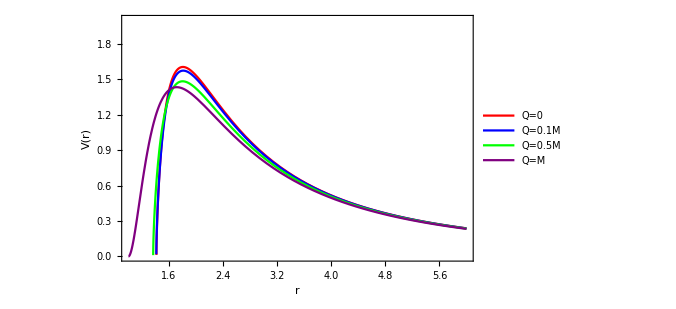

```mathematica
PlotPotential
```

```mathematica
QNMModeComp :=Module[{SeedValue,barλ,f,CC,AA,BB,W1,W2,W3,W,V,G,DiffV,R,r,r0,Q,Z0,k,b,S,ω,A,TotQ},
TotDim=9;
Do[Subscript[AA, l]=Table[{-Im[WKBSeed[l,n,0,TotDim]],Re[WKBSeed[l,n,0,TotDim]]} ,{n,0,l}],{l,0,5}];
Do[Subscript[GG, l] =Table[{-Im[WKBSeed[l,n,0.1,TotDim]],Re[WKBSeed[l,n,0.1,TotDim]]},{n,0,l}],{l,0,5}];
Do[Subscript[HH, l] =Table[{-Im[WKBSeed[l,n,0.5,TotDim]],Re[WKBSeed[l,n,0.5,TotDim]]},{n,0,l}],{l,0,5}];
Do[Subscript[LL, l] =Table[{-Im[WKBSeed[l,n,1,TotDim]],Re[WKBSeed[l,n,1,TotDim]]},{n,0,l}],{l,0,5}];
Print[ListLinePlot[{Subscript[AA, 0],Subscript[GG, 0],Subscript[HH, 0],Subscript[LL, 0],Subscript[AA, 1],Subscript[GG, 1],Subscript[HH, 1],Subscript[LL, 1],Subscript[AA, 2],Subscript[GG, 2],Subscript[HH, 2],Subscript[LL, 2],Subscript[AA, 3],Subscript[GG, 3],Subscript[HH, 3],Subscript[LL, 3],Subscript[AA, 4],Subscript[GG, 4],Subscript[HH, 4],Subscript[LL, 4],Subscript[AA, 5],Subscript[GG, 5],Subscript[HH, 5],Subscript[LL, 5]},PlotRange->{0,1.5}ImageSize->500,Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"Re(ω)",None},{"Im(ω)",None}},FrameTicks->All,PlotStyle->{Black,Red,Blue,Green,Black,Red,Blue,Green,Black,Red,Blue,Green,Black,Red,Blue,Green,Black,Red,Blue,Green,Black,Red,Blue,Green},ImageSize->500,Axes->False,Frame->{{True,False},{True,False}},FrameTicks->All,PlotLegends-> {"Q=0","Q=0.1","Q=0.5","Q=1"},PlotMarkers->"■"]]]
```

```mathematica
(*QNMModeComp*)
```

```mathematica
AbsorptionFunction[l_,TotQ_,TotDim_,ω_] := Module[{SeedValue,barλ,f,CC,AA,BB,W1,W2,W3,W,V,G,DiffV,R,r,r0,Q,Z0,k,b,S,A,Ω,TotM=1},
SeedValue=WKBSeed[l,0,TotQ,TotDim] ;
barζ= (l+3/2)+(TotDim-3)/(2); (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))+(TotQ^(2)/r^(2*TotDim -6)); (*Metric function*)
           (*Paste potential between these two comments*)
        W[r_] =(barζ*Sqrt[f[r]])/(r)-((TotQ*Sqrt[f[r]])/(2*r^(TotDim-2)))(TotDim-2);
V[r_] =f[r]*D[W[r],r]+(W[r])^(2);(* non-TT potential*)
(*Paste potential here *)
DiffV[r_] = D[V[r],r];
r0=First[Sort[r/.NSolve[{DiffV[r]==0&&(1.3≤ r < 3)},r,Reals],Greater]];(*Our r0 values seem to have a maximum of 2.5. r0 going from zero to four here is to reduce computation time*)(*This may have to change for diffirent values of M*)
Q[0][r_,Ω_]=Ω^2-V[r];
Q[1][r_,Ω_]=Simplify[ f[r]×D[Q[0][r,Ω],r]];
Do[Q[q+1][r_,Ω_]=Simplify[ f[r]×D[Q[q][r,Ω],r]],{q,1,7}];
Z0[Ω_]=Simplify[ Sqrt[-2*(Q[0][r0,Ω]/Q[2][r0,Ω])]];
k [Ω_] = Simplify[(1/2)(Q[2][r0,Ω])];
Do[b[i][Ω_] = (2/(Factorial[i]*(Q[2][r0,Ω])))(Q[i][r0,Ω]);,{i,3,6}];
S[Ω_] = Simplify[π k[Ω]^(1/2) (Z0[Ω]^2/2+(15/64 (b[3][Ω])^2-(3 b[4][Ω])/16) Z0[Ω]^4)+π √k[Ω] ((1155 (b[3][Ω])^4)/2048-315/256 (b[3][Ω])^2 b[4][Ω]+35/128 (b[4][Ω])^2+35/64 b[3][Ω] b[5][Ω]-(5 b[6][Ω])/32) Z0[Ω]^6+π 1/(√k[Ω]) ((3 b[4][Ω])/16-7/64 (b[3][Ω])^2)-π 1/(√k[Ω]) ((1365 (b[3][Ω])^4)/2048-525/256 (b[3][Ω])^2 b[4][Ω]+85/128 (b[4][Ω])^2+95/64 b[3][Ω] b[5][Ω]-(25 b[6][Ω])/32) Z0[Ω]^2];
Return[ 1/(1 + Exp[2*S[ω]])];];
```

```mathematica
AbsorptionProbablities:= Module[{SeedValue,barλ,f,CC,AA,BB,W1,W2,W3,W,V,G,DD,DiffV,R,r,r0,Q,Z0,k,b,S,ω,A,TotQ},
TotDim=7;
Do[AA[l][ω_]=AbsorptionFunction[l,0,TotDim,ω];
Print[AA[l][ω]];,{l,0,2}];
Do[BB[l][ω_]=AbsorptionFunction[l,0.1,TotDim,ω];
Print[BB[l][ω]];,{l,0,2}];
Do[CC[l][ω_]=AbsorptionFunction[l,0.5,TotDim,ω];
Print[CC[l][ω]];,{l,0,2}];
Do[DD[l][ω_]=AbsorptionFunction[l,1,TotDim,ω];
Print[DD[l][ω]];,{l,0,2}];
Print[DD[4][0]];
Print[Plot[{-1,-1,-1,-1,-1(*AA[0][ω]*),BB[0][ω],CC[0][ω],DD[0][ω],AA[1][ω],BB[1][ω],CC[1][ω],DD[1][ω],AA[2][ω],BB[2][ω],CC[2][ω],DD[2][ω]},{ω,0,4.5},ImageSize->500,PlotRange->{0,1},Frame->True,FrameLabel->{{Style["|A(ω)|^2",18,Black],None},{Style["ω",18,Black],None}},LabelStyle-> "Times New Roman",FrameTicksStyle->14,PlotStyle-> {Red,Blue,Green,Purple,Directive[Red,Dotted],Directive[Blue,Dotted],Directive[Green,Dotted],Directive[Purple,Dotted],Directive[Red,Dashed],Directive[Blue,Dashed],Directive[Green,Dashed],Directive[Purple,Dashed],Red,Blue,Green,Purple,Red,Blue,Green,Purple,Red,Blue,Green,Purple,Red,Blue,Green,Purple},ImageSize->500,Axes->False,PlotLegends-> Placed[{Style["Q=0",FontSize->16],Style["Q=0.1",FontSize->16],Style["Q=0.5",FontSize->16],Style["Q=1",FontSize->16]},Right]]]];
```

1/(1+ⅇ^(2 (4.22009-1.86563 ω$5103^2+0.220244 ω$5103^4-0.013087 ω$5103^6)))

1/(1+ⅇ^(2 (5.57988-1.51821 ω$5103^2+0.114662 ω$5103^4-0.00428111 ω$5103^6)))

1/(1+ⅇ^(2 (6.90471-1.26912 ω$5103^2+0.0659086 ω$5103^4-0.00168075 ω$5103^6)))

1/(1+ⅇ^(2 (4.20606-1.9027 ω$5103^2+0.229808 ω$5103^4-0.0139607 ω$5103^6)))

1/(1+ⅇ^(2 (5.56665-1.54213 ω$5103^2+0.118599 ω$5103^4-0.0045063 ω$5103^6)))

1/(1+ⅇ^(2 (6.89263-1.28571 ω$5103^2+0.0677726 ω$5103^4-0.00175346 ω$5103^6)))

1/(1+ⅇ^(2 (4.18169-2.06023 ω$5103^2+0.271102 ω$5103^4-0.0178574 ω$5103^6)))

1/(1+ⅇ^(2 (5.56731-1.64591 ω$5103^2+0.135184 ω$5103^4-0.00546988 ω$5103^6)))

1/(1+ⅇ^(2 (6.91691-1.3585 ω$5103^2+0.0754305 ω$5103^4-0.00205262 ω$5103^6)))

1/(1+ⅇ^(2 (4.08128-2.20281 ω$5103^2+0.318273 ω$5103^4-0.0229016 ω$5103^6)))

1/(1+ⅇ^(2 (5.60319-1.7815 ω$5103^2+0.158111 ω$5103^4-0.00687074 ω$5103^6)))

1/(1+ⅇ^(2 (7.09743-1.47685 ω$5103^2+0.0873912 ω$5103^4-0.00251589 ω$5103^6)))

DD$5103[4][0]

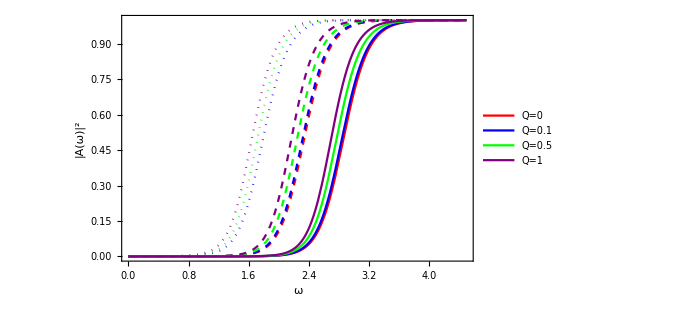

```mathematica
AbsorptionProbablities
```

```mathematica
Quit[];(*Always make sure this is the last command Mathematica executes*)
```

Various routines for plotting potential function comparisons.

```mathematica
PlotPotentialDim[TotDim_,TotQ_,MaxY_,MaxX_]:=Module[{R,l},
Do[TotΛ=0;
barζ= (l+3/2)+(TotDim-3)/(2); (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))-((2*TotΛ*r^(2))/((TotDim-2)(TotDim-1)))+((TotQ^(2))/r^(2*TotDim -6)); (*Eigenvalues for the sphere*)
(*Paste potential between these two comments*)
 W[r_] =(barζ*Sqrt[f[r]])/(r)-((TotQ*Sqrt[f[r]])/(2*r^(TotDim-2)))(TotDim-2);
Subscript[V, l][r_] =f[r]*D[W[r],r]+(W[r])^(2);,{l,0,5}];
Print[Plot[{Subscript[V, 0][R],Subscript[V, 1][R],Subscript[V, 2][R],Subscript[V, 3][R],Subscript[V, 4][R],Subscript[V, 5][R]},{R,0,MaxX},ImageSize->500,Frame->True,FrameLabel->{{"V(r)",None},{"r",None}},PlotRange->{0,MaxY},PlotLegends->{"3/2","5/2","7/2","9/2","11/2","13/2"}]]];
```

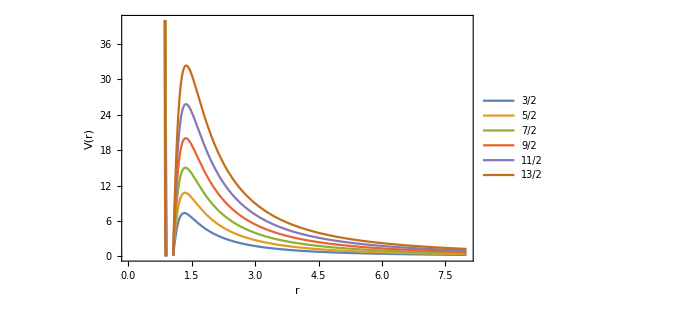

```mathematica
PlotPotentialDim[9,0.9,40,8]
```

```mathematica
PlotPotentialDim[TotDim_,TotQ_,MaxY_,MaxX_]:=Module[{R,l,EventLine},
Do[barζ= (l+3/2)+(TotDim-3)/(2); (*Eigenvalues for the sphere*)
f[r_] := 1 - ((2*TotM)/(r)^(TotDim-3))-((2*TotΛ*r^(2))/((TotDim-2)(TotDim-1)))+((TotQ^(2))/r^(2*TotDim -6)); (*Eigenvalues for the sphere*)
(*Paste potential between these two comments*)
 W[r_] =(barζ*Sqrt[f[r]])/(r)-((TotQ*Sqrt[f[r]])/(2*r^(TotDim-2)))(TotDim-2);
Subscript[V, l][r_] =f[r]*D[W[r],r]+(W[r])^(2);
(*Paste potential here *),{l,0,5}];
EventLine=Line[{{(TotM+Sqrt[TotM^(2)-TotQ^(2)])^(1/(TotDim-3)),0},{(TotM+Sqrt[TotM^(2)-TotQ^(2)])^(1/(TotDim-3)),MaxY}}];
Print[Plot[{Subscript[V, 0][R],Subscript[V, 1][R],Subscript[V, 2][R],Subscript[V, 3][R],Subscript[V, 4][R],Subscript[V, 5][R]},{R,0,MaxX},ImageSize->500,FrameTicksStyle->14,PlotLegends->{Style["3/2",FontSize->16],Style["5/2",FontSize->16],Style["7/2",FontSize->16],Style["9/2",FontSize->16],Style["11/2",FontSize->16],Style["13/2",FontSize->16]},Frame-> True,FrameLabel->{{Style["V(r)",FontSize->18,Black],None},{Style["r",FontSize->18,Black],None}},PlotRange->{{(TotM+Sqrt[TotM^(2)-TotQ^(2)])^(1/(TotDim-3))-1,MaxX},{0,MaxY}},Epilog->{Directive[Red,Dashed,Thick],EventLine}]]];
```

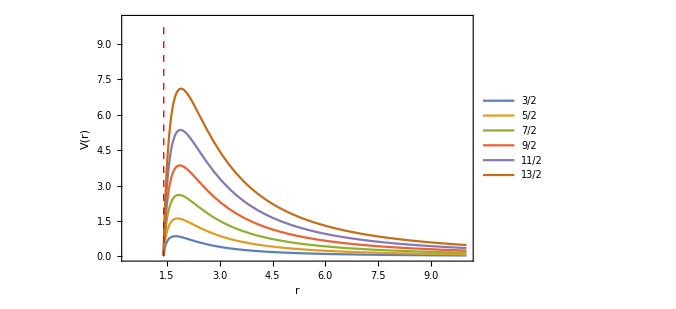

```mathematica
PlotPotentialDim[5,0,10,10]
```